```mathematica
net=NetInitialize[
LinearLayer[4,"Input"->2],
Method->{"Random","Weights"->2,"Biases"->2}
]
```

LinearLayer[<>]

### Does every neuron have a bias?

```mathematica
NetInformation[net,"Arrays"]
```

```mathematica
<|{"Biases"}->{2.2264106273651123,1.753065586090088,-0.36508670449256897,-0.26166048645973206},
{"Weights"}->{{-2.9367456436157227,-1.4741079807281494},{1.6393293142318726,1.0153454542160034},{-1.9557093381881714,3.5741984844207764},{0.9360641241073608,-0.7353979349136353}}|>
```

```mathematica
magnum
```

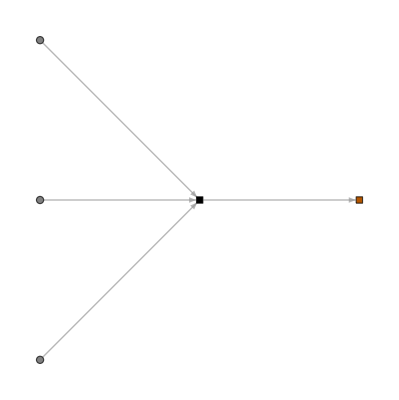

```mathematica
NetInformation[net,"MXNetNodeGraph"]
```

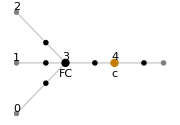

```mathematica
NetInformation[net,"MXNetNodeGraphPlot"]
```